## Equation solver for stationary quantizer Maria

### Define equations

```mathematica
Clear[gammaList,eqList,probList,solutions,gammaVector,gammaSol,gamma,probSol,probabilities, γ]
```

```mathematica
n={1,2,3,4,5,6,7,8,9,10,11};
Nmax =2^n[[11]];(*Change this to set the number of bins*)
EvenBins = "True" ;(*Change boundary conditions for even or odd number of bins*)
```

```mathematica
prob[n_]:=(1/2) (Erf[(γ[n+1]+γ[n])/(2Sqrt[2])]-Erf[(γ[n-1]+γ[n])/(2Sqrt[2])]);
```

```mathematica
eq[n_]:=γ[n]== (Exp[-((γ[n-1]+γ[n])^2)/8 ]-  Exp[-((γ[n+1]+γ[n])^2)/8])/(Sqrt[2 π]prob[n]);
```

```mathematica
gammaList={{γ[0],0}};
probList = {Erf[γ[1]/(2 Sqrt[2])]};

If[ EvenBins == "True",
eqList = {γ[0] == -γ[1]};
numberBins = 2*Nmax;,
eqList = {γ[0]==0.};
numberBins = 2*Nmax + 1;
]

Do[
gammaList=Append[gammaList,{γ[n],3n/Nmax}];
probList = Append[probList,prob[n]];
eqList = Append[eqList,eq[n]],
{n,1,Nmax-1,1}]
```

```mathematica
(*Calculate the last elements with boundary condition γ[Nmax+1] = Inf*)
```

```mathematica
gammaList = Append[gammaList,{γ[Nmax],3}];
```

```mathematica
probList = Append[probList, (1/2)(1 - Erf[(γ[Nmax]+γ[Nmax-1])/(2Sqrt[2])])];
```

```mathematica
eqList = Append[eqList,γ[Nmax]==Exp[-((γ[Nmax-1]+γ[Nmax])^2)/8]/(Sqrt[2π]probList[[Nmax+1]]) ];
```

### Find and organize solutions

```mathematica
solutions = FindRoot[eqList,gammaList];
```

Power::infy: Infinite expression 1/0. encountered.

FindRoot::nlnum: The function value {0.,1.78693×10^-12,5.40123×10^-12,9.00486×10^-12,1.25498×10^-11,1.62125×10^-11,1.9875×10^-11,2.34153×10^-11,2.69605×10^-11,3.0619×10^-11,«2039»} is not a list of numbers with dimensions {2049} at {γ[0],γ[1],γ[2],γ[3],γ[4],γ[5],γ[6],γ[7],γ[8],γ[9],«2039»} = {-0.00061324,0.00061324,0.00183972,0.0030662,0.00429268,0.00551917,0.00674565,0.00797214,0.00919864,0.0104251,«2039»}.

```mathematica
gammaVector ={};
Do[
gammaVector = Append[gammaVector,γ[n]],
{n,0,Nmax,1}];

gammaSol = gammaVector/.solutions;
probSol = probList/.solutions;
```

```mathematica
(*If number of bins is even, you need to get rid of γ[0]*)
If[ EvenBins == "True",
gammaSol = Drop[gammaSol,1];
probSol = Drop[probSol,1];,
gammaSol;
probSol;
]
```

```mathematica
gamma = Join[Reverse[Take[-gammaSol, -Nmax]],gammaSol];
```

```mathematica
probabilities = Join[Reverse[Take[probSol, -Nmax]],probSol];
```

```mathematica
test = Total[probabilities]; (*Should be =1*)
```

### Plot

```mathematica
plotList = {};
Do[
plotList=Append[plotList,{gamma[[n]],probabilities[[n]]}]
,{n,1,Length[gamma],1}];
```

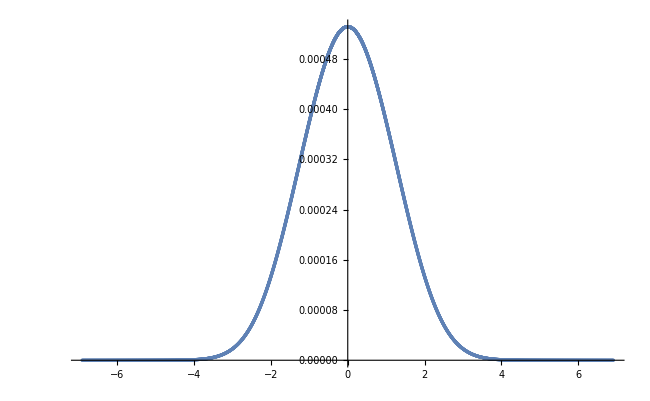

```mathematica
ListPlot[plotList]
```

### Print on file (load in Python)

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
numFormat[y_]:=ToString@NumberForm[y,{16,16},ExponentFunction->(If[-14<#<14,Null,#]&)];
numberStr=Map[numFormat,probabilities];
```

```mathematica
Export[StringJoin["probabilities_NBins_",ToString[numberBins],".txt"],numberStr]
```

probabilities_NBins_4096.txt

```mathematica
Export[StringJoin["gammas_NBins_",ToString[numberBins],".txt"],gamma]
```

gammas_NBins_4096.txt